# Chapter 4 Lab 2: Contour Tangents

Work in-Class activity Chapter 4 Activity 1 Contours.nb

Copy and paste your solutions into this NoteBook in a tidy form.

Save your final work on your account and submit your solution to the Engineering Math 2 Digital Dropbox with a file name in the form

LastNameFirstNameCh#Lab#.nb 
(no spaces or other characters)

for example, StroyanKeithCh3Lab2.nb

## Jamel Lamel & T.A. Colin

f[x,y]=Cos[x^2-x]/(1+y^2)-1/2 x Sin[3 y]

a)  Draw the contour of the function f[x,y] through the point (x,y)=(2,1).

```mathematica
fX[x_,y_]=D[f[x,y],x]
fY[x_,y_]=D[f[x,y],y]
gradf[x_,y_]={fX[x,y],fY[x,y]}
```

Cos[x-x^2]/(1+y^2)-1/2 x Sin[3 y]

Cos[2]/2-Sin[3]

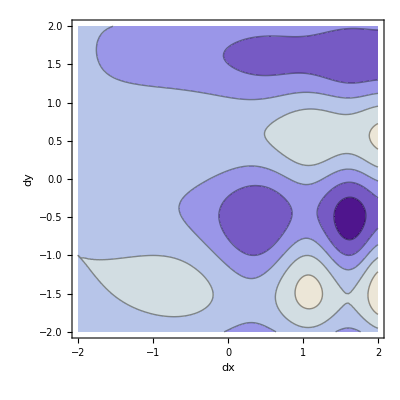

```mathematica
Clear[x,y,dx,dy,f,fX,fY,gradf];
Needs["iMultiCalc`iMCUtilities`"]
f[x_,y_]=Cos[x^2- x]/(1 + y^2) - (x/2)Sin[3y]
x=2;
y=1;
z=f[x,y]
δ=2;
contours=ContourPlot[f[x+dx,y+dy],{dx,-δ,δ},{dy,-δ,δ},FrameLabel->{"dx","dy"}]
```

b)  Compute the implicit equation of the line tangent to this contour at this point.

```mathematica
x=2;
y=1;
z=f[x,y]
δ=2;
contours=ContourPlot[f[x+dx,y+dy],{dx,-δ,δ},{dy,-δ,δ},FrameLabel->{"dx","dy"}]
```

c)  Plot the tangent line.

```mathematica
x=2;
y=1;
z=f[x,y];
δ=1/10;

singleCurve=ContourPlot[f[x+dx,y+dy]==f[x,y],{dx,-δ,δ},{dy,-δ,δ},ContourStyle->{AbsoluteThickness[2],Green},FrameLabel->{"dx","dy"}];

singleLine=ContourPlot[dz[dx,dy]==0,{dx,-δ,δ},{dy,-δ,δ},ContourStyle->{AbsoluteThickness[2],Magenta},FrameLabel->{"dx","dy"}];

Show[{dFrame2D[δ],singleCurve,singleLine,Arrow2D[gradf[x,y]/30,Orange]}]
```

d) Show both plots together in the same coordinates.

HINT:  Your solution should look something like at least one of the following.